```mathematica
Table[i,{i,0,40,2}]
```

{0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40}

```mathematica
Table[Fibonacci[n],{n,1,16}]
```

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987}

```mathematica
Table[i,{i,1,39,2}]
```

{1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39}

```mathematica
Table[Prime[n],{n,1,25}]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

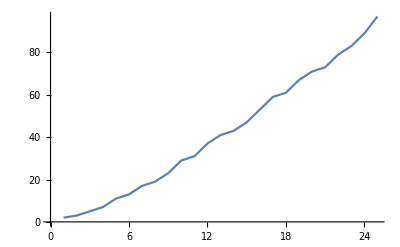

```mathematica
ListLinePlot[{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}]
```

```mathematica
x=Cos[t];
y=Sin[t];
Table[{x,y},{t,0,2Pi,0.1}]
```

{{1.,0.},{0.995004,0.0998334},{0.980067,0.198669},{0.955336,0.29552},{0.921061,0.389418},{0.877583,0.479426},{0.825336,0.564642},{0.764842,0.644218},{0.696707,0.717356},{0.62161,0.783327},{0.540302,0.841471},{0.453596,0.891207},{0.362358,0.932039},{0.267499,0.963558},{0.169967,0.98545},{0.0707372,0.997495},{-0.0291995,0.999574},{-0.128844,0.991665},{-0.227202,0.973848},{-0.32329,0.9463},{-0.416147,0.909297},{-0.504846,0.863209},{-0.588501,0.808496},{-0.666276,0.745705},{-0.737394,0.675463},{-0.801144,0.598472},{-0.856889,0.515501},{-0.904072,0.42738},{-0.942222,0.334988},{-0.970958,0.239249},{-0.989992,0.14112},{-0.999135,0.0415807},{-0.998295,-0.0583741},{-0.98748,-0.157746},{-0.966798,-0.255541},{-0.936457,-0.350783},{-0.896758,-0.44252},{-0.8481,-0.529836},{-0.790968,-0.611858},{-0.725932,-0.687766},{-0.653644,-0.756802},{-0.574824,-0.818277},{-0.490261,-0.871576},{-0.400799,-0.916166},{-0.307333,-0.951602},{-0.210796,-0.97753},{-0.112153,-0.993691},{-0.0123887,-0.999923},{0.087499,-0.996165},{0.186512,-0.982453},{0.283662,-0.958924},{0.377978,-0.925815},{0.468517,-0.883455},{0.554374,-0.832267},{0.634693,-0.772764},{0.70867,-0.70554},{0.775566,-0.631267},{0.834713,-0.550686},{0.88552,-0.464602},{0.927478,-0.373877},{0.96017,-0.279415},{0.983268,-0.182163},{0.996542,-0.0830894}}

```mathematica
x=Cos[t];
y=Sin[t];
ListLinePlot[
Table[{x,y},{t,0,2Pi,0.1}],
PlotStyle->{Thick,Black},
AspectRatio->1,
PlotTheme->"Marketing",
Background->Green
]
```

-Graphics-

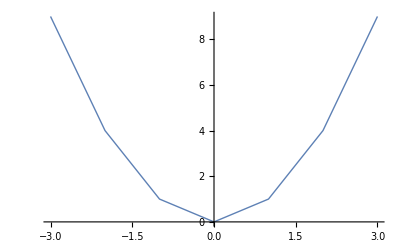

```mathematica
ListLinePlot[
Table[{x,x^2},{x,-3,3,1}],
PlotStyle->Thick
]
```

```mathematica
?InterpolationOrder
```

InterpolationOrder is an option for Interpolation, as well as ListLinePlot, ListPlot3D, ListContourPlot, and related functions, that specifies what order of interpolation to use.

```mathematica
Table[ListPlot3D[
Table[{x,x^2} ,{x,-3,3,1}],
InterpolationOrder->n],
{n,{0,1,2}}
]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}